# Aliasing

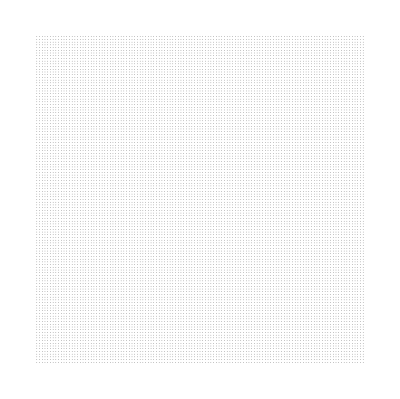

```mathematica
r = 0.1;
n=60;
dx = 0.0;
coords = Flatten[Table[{i + j Cos[90. Degree], Sin[90. Degree]j}, {j, -n ,n}, {i, -n, n}],1];
shiftCoords = Flatten[Table[{RandomReal[{-dx,dx}],RandomReal[{-dx,dx}]}, {j, -n ,n}, {i, -n, n}],1];
graph = Graphics[Disk[#, r]&/@(coords+shiftCoords)]
```

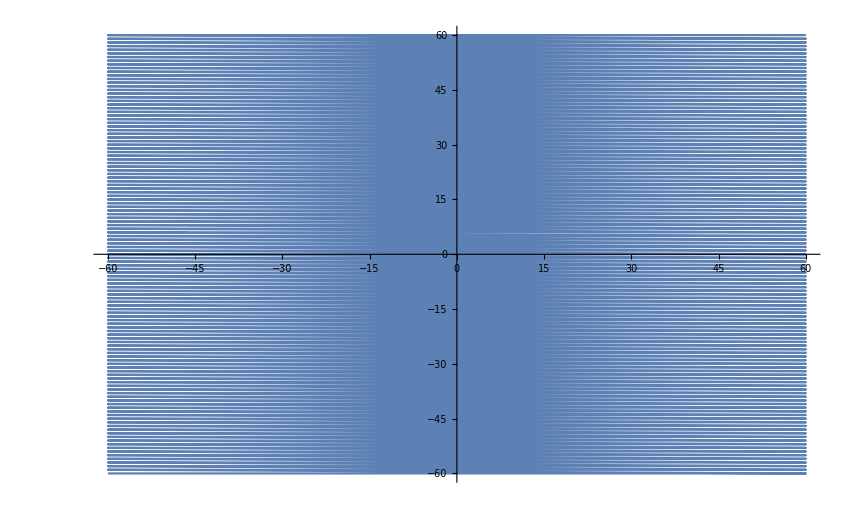

```mathematica
ListPlot[coords, Joined->True]
```

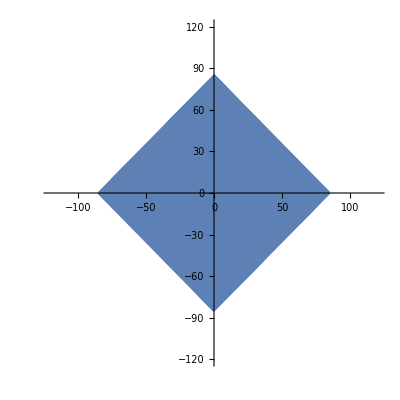

```mathematica
ListPlot[coords.RotationMatrix[Pi/4.], Joined->True, PlotRange->{{-2 n, 2 n}, {-2 n, 2 n}},AspectRatio->1]
```

```mathematica
Manipulate[

Show[Graphics[Disk[#, r]&/@((coords + shiftCoords).RotationMatrix[phi].ScalingMatrix[{k, k}]),ImageSize->Full],graph],
{phi, 0, 4 Pi},
{{k, 1}, 0, 2}
]
```

Thread::tdlen: Objects of unequal length in … cannot be combined.

# Bezier curves

```mathematica
x = Range[0, 10];
y=Range[0, 10]^(3/2)//N;
coords = Transpose[{x, y}]
```

{{0,0.},{1,1.},{2,2.82843},{3,5.19615},{4,8.},{5,11.1803},{6,14.6969},{7,18.5203},{8,22.6274},{9,27.},{10,31.6228}}

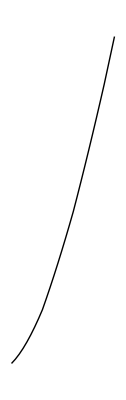

```mathematica
Graphics@BezierCurve[coords]
```

# Fourier transform of 2d surface

```mathematica
n=20;
r=10;
coords3D = Flatten[Table[{i, j, If[i^2+j^2<r^2,1, 0]},{j, -n, n},{i, -n, n}],1]
```

{{-20,-20,0},{-19,-20,0},{-18,-20,0},{-17,-20,0},{-16,-20,0},{-15,-20,0},{-14,-20,0},{-13,-20,0},{-12,-20,0},{-11,-20,0},{-10,-20,0},{-9,-20,0},{-8,-20,0},{-7,-20,0},{-6,-20,0},{-5,-20,0},{-4,-20,0},{-3,-20,0},{-2,-20,0},{-1,-20,0},{0,-20,0},{1,-20,0},{2,-20,0},{3,-20,0},{4,-20,0},{5,-20,0},{6,-20,0},{7,-20,0},{8,-20,0},{9,-20,0},{10,-20,0},{11,-20,0},{12,-20,0},{13,-20,0},{14,-20,0},{15,-20,0},{16,-20,0},{17,-20,0},{18,-20,0},{19,-20,0},{20,-20,0},{-20,-19,0},{-19,-19,0},{-18,-19,0},1593,{18,19,0},{19,19,0},{20,19,0},{-20,20,0},{-19,20,0},{-18,20,0},{-17,20,0},{-16,20,0},{-15,20,0},{-14,20,0},{-13,20,0},{-12,20,0},{-11,20,0},{-10,20,0},{-9,20,0},{-8,20,0},{-7,20,0},{-6,20,0},{-5,20,0},{-4,20,0},{-3,20,0},{-2,20,0},{-1,20,0},{0,20,0},{1,20,0},{2,20,0},{3,20,0},{4,20,0},{5,20,0},{6,20,0},{7,20,0},{8,20,0},{9,20,0},{10,20,0},{11,20,0},{12,20,0},{13,20,0},{14,20,0},{15,20,0},{16,20,0},{17,20,0},{18,20,0},{19,20,0},{20,20,0}}
 |  |  |  |

```mathematica
ListPointPlot3D[coords3D, Filling->Bottom]
```

-Graphics3D-

```mathematica
f=Interpolation[coords3D]
```

InterpolatingFunction[…]

```mathematica
f[1, 3.3]
```

1.

```mathematica
freq3D=Fourier[coords3D,FourierParameters->{1,1}];
```

```mathematica
ListPointPlot3D[Abs[freq3D], PlotRange->All]
```

-Graphics3D-

```mathematica
fudgeFactor=100;
abs=fudgeFactor*Log[1+Abs@freq3D];
Labeled[Image[abs/Max[abs]],Style["Magnitude spectrum",18]]
```

-Graphics-Magnitude spectrum

```mathematica
img=ColorConvert[Import["ExampleData/lena.tif"],"Grayscale"]
```

-Graphics-

```mathematica
(abs=Abs[Fourier[ImageData[img]]])//Image
(arg=Arg[Fourier[ImageData[img]]])//Image
```

-Graphics-

-Graphics-

# Fractal tree

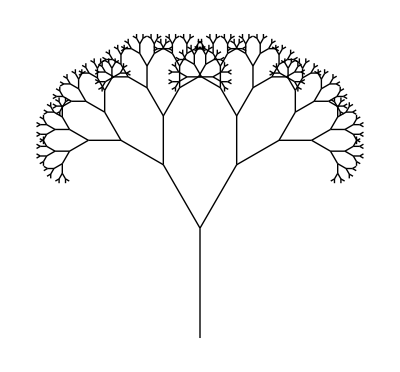

```mathematica
ClearAll[next];

next[{{x1_,y1_},{x2_,y2_}}]=({{x1,y1},{x2,y2}}//TranslationTransform[{x2-x1,y2-y1}]//RotationTransform[# Pi/6,{x2,y2}]//ScalingTransform[2/3 {1,1},{x2,y2}])&/@{-1,1};

list=NestList[Join@@next/@#&,N@{{{0,0},{0,1}}},8];

Graphics[Line/@list]
```

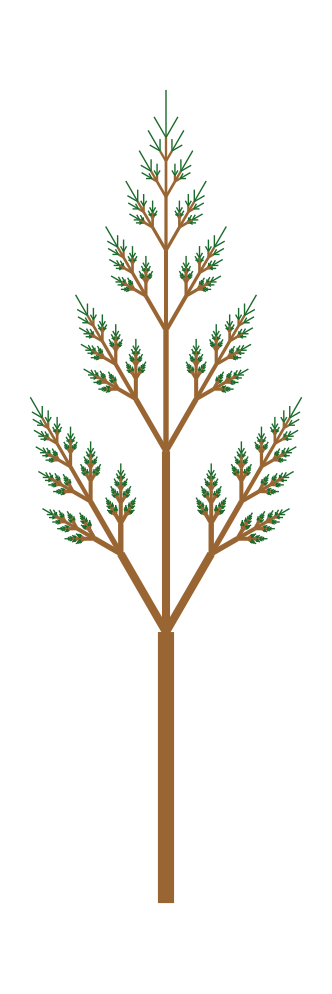

```mathematica
θ=Pi/6;
mz={{Cos[θ],-Sin[θ]},{Sin[θ],Cos[θ]}};
my={{Cos[-θ],-Sin[-θ]},{Sin[-θ],Cos[-θ]}};

iterate[leaf[{b_,a_,k_}]]:=Module[
{c,d,e},
c=1/3*a+2/3*b;
d=c+mz.(a-b)*(1/3);
e=c+my.(a-b)*(1/3);
{
branch[{b,c,k+1}],
leaf[{c,a,k+1}],
leaf[{c,d,k+1}],
leaf[{c,e,k+1}]
}
]

iterate[b_branch]:=b

tree=Nest[
Flatten[iterate/@#]&,
{leaf[{{0.,0.},{0.,1.},0}]},
7
];

Graphics[{Brown,Cases[tree,branch[{x_,y_,k_}]:>{Thickness[0.035/k],Line[{x,y}]}],RGBColor[0.1,0.42,0.17],Cases[tree,leaf[{x_,y_,k_}]:>Line[{{x,y}}]]}]
```

```mathematica
Nest[Sin, z, 3]/.z->Pi/2//N
```

0.745624

```mathematica
Limit[Nest[Sin, 1, n],n->Infinity]
```

Limit::ivar: 20 is not a valid variable.

lim_(20→∞) Sin[Sin[Sin[Sin[Sin[Sin[Sin[Sin[Sin[Sin[Sin[Sin[Sin[Sin[Sin[Sin[Sin[Sin[Sin[Sin[1]]]]]]]]]]]]]]]]]]]]

```mathematica
ListPlot[Nest[Sin, 1, #]&/@Range[1, 10000], PlotRange->All]
```

$Aborted